```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
```

# SimplePass

# 数据处理

```mathematica
data=Import[NotebookDirectory[]<>"..\\data\\2020_Problem_D_DATA\\fullevents.csv"];
```

```mathematica
object=Transpose[data][[{3,4,8}]];
```

```mathematica
myteam=Drop[Thread[Table[object[[i]],{i,1,3}]],1];
```

# 函数

```mathematica
function1[alpha_]:=Cases[alpha,{x_,y_,z_}/;(If[x=="",False,StringSplit[x,"_"][[1]]=="Huskies"]||If[y=="",False,StringSplit[y,"_"][[1]]=="Huskies"])&&z!="Simple pass"]
```

```mathematica
function2[beta_]:=Cases[beta,{x_,y_,z_}/;(If[x=="",False,StringSplit[x,"_"][[1]]=="Huskies"]||If[y=="",False,StringSplit[y,"_"][[1]]=="Huskies"])]
```

```mathematica
Length@function1[myteam]
```

18045

```mathematica
Length@function2[myteam]
```

28217

```mathematica
Length@function1[myteam]/Length@function2[myteam]//N
```

0.639508

```mathematica
functionnew1[alpha_,member_]:=Cases[alpha,{x_,y_,z_}/;(If[x=="",False,x==member]||If[y=="",False,y==member])&&z!="Simple pass"]
```

```mathematica
functionnew2[alpha_,member_]:=Cases[alpha,{x_,y_,z_}/;If[x=="",False,x==member]||If[y=="",False,y==member]]
```

```mathematica
Length@functionnew1[myteam,"Huskies_D1"]/Length@functionnew2[myteam,"Huskies_D1"]
```

253/530

```mathematica
functionnew2[myteam,"Huskies_D1"]
```

{{Huskies_D1,Huskies_F1,Head pass},{Huskies_D1,,High pass},{Huskies_D1,Huskies_F1,Head pass},{Huskies_D1,Huskies_G1,Simple pass},{Huskies_D1,,Ground loose ball duel},{Huskies_D1,,Touch},{Huskies_D1,,Ground defending duel},{Huskies_D1,,Throw in},{Huskies_D1,Huskies_D2,Simple pass},{Huskies_D1,,Air duel},{Huskies_D1,,Touch},{Huskies_D1,Huskies_M3,Simple pass},{Huskies_G1,Huskies_D1,Hand pass},2624,{Huskies_F6,Huskies_D1,Simple pass},{Huskies_D1,Huskies_D3,Simple pass},{Huskies_D1,,Clearance},{Huskies_D1,,Touch},{Huskies_D1,,Air duel},{Huskies_D1,,Air duel},{Huskies_D1,Huskies_M1,Head pass},{Huskies_D1,,Head pass},{Huskies_F6,Huskies_D1,Simple pass},{Huskies_D1,Huskies_M1,Simple pass},{Huskies_D1,,Ground defending duel},{Huskies_D1,,Ground defending duel},{Huskies_D1,,Air duel}}
 |  |  |  |

# 测试

```mathematica
fraction[gammar_,member_]:=Length@functionnew1[gammar,member]/Length@functionnew2[gammar,member]
```

```mathematica
fractionmyteam[member_]:=fraction[myteam,member]
```

```mathematica
fractionmyteam["Huskies_D1"]
```

253/530

# Member

```mathematica
allmember=Table["Huskies_"<>"F"<>ToString[i],{i,1,6}]~Join~Table["Huskies_"<>"M"<>ToString[i],{i,1,13}]~Join~
Table["Huskies_"<>"D"<>ToString[i],{i,1,10}]~Join~
Table["Huskies_"<>"G"<>ToString[i],{i,1,1}]
```

{Huskies_F1,Huskies_F2,Huskies_F3,Huskies_F4,Huskies_F5,Huskies_F6,Huskies_M1,Huskies_M2,Huskies_M3,Huskies_M4,Huskies_M5,Huskies_M6,Huskies_M7,Huskies_M8,Huskies_M9,Huskies_M10,Huskies_M11,Huskies_M12,Huskies_M13,Huskies_D1,Huskies_D2,Huskies_D3,Huskies_D4,Huskies_D5,Huskies_D6,Huskies_D7,Huskies_D8,Huskies_D9,Huskies_D10,Huskies_G1}

```mathematica
allmemberlist=Table[List[allmember[[i]],allmember[[j]]],{i,1,30},{j,1,30}];
```

```mathematica
a=fractionmyteam/@allmember
```

{253/327,1183/2861,131/251,803/1106,607/903,629/1053,1327/3566,95/236,308/821,931/1913,71/152,1109/2101,21/61,374/713,365/642,113/192,45/104,7/11,108/235,253/530,805/1759,933/2102,809/1957,1153/2228,230/423,1016/1777,604/1103,52/145,71/133,499/703}

```mathematica
a//N
```

{0.7737,0.413492,0.521912,0.72604,0.672204,0.597341,0.372126,0.402542,0.375152,0.48667,0.467105,0.527844,0.344262,0.524544,0.568536,0.588542,0.432692,0.636364,0.459574,0.477358,0.457646,0.443863,0.413388,0.517504,0.543735,0.57175,0.547597,0.358621,0.533835,0.709815}

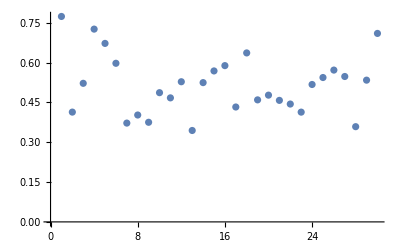

```mathematica
ListPlot[a]
```

# Distances

# 数据处理

```mathematica
data2=Import[NotebookDirectory[]<>"..\\data\\2020_Problem_D_DATA\\passingevents.csv"];
```

```mathematica
object2=Transpose[data2][[{2,3,4,8,9,10,11}]];
```

```mathematica
team2=Drop[Thread[Table[object2[[i]],{i,1,7}]],1];
```

```mathematica
myteamfn=Cases[team2,{"Huskies",_,_,_,_,_,_}]
```

{{Huskies,Huskies_D1,Huskies_F1,34,97,59.,95.},{Huskies,Huskies_M1,Huskies_F2,53,89,69.,91.},{Huskies,Huskies_M2,Huskies_M3,42,55,36.,54.},{Huskies,Huskies_D1,Huskies_F1,34,91,52.,97.},{Huskies,Huskies_D1,Huskies_G1,14,65,11.,50.},{Huskies,Huskies_G1,Huskies_G1,11,50,5.,45.},{Huskies,Huskies_D1,Huskies_D2,17,92,22.,62.},{Huskies,Huskies_D2,Huskies_D3,22,62,19.,24.},{Huskies,Huskies_D3,Huskies_G1,19,24,8.,45.},10418,{Huskies,Huskies_D1,Huskies_M1,55,45,64.,71.},{Huskies,Huskies_M1,Huskies_M12,64,71,78.,91.},{Huskies,Huskies_M1,Huskies_D4,56,80,66.,15.},{Huskies,Huskies_D4,Huskies_F6,66,15,62.,23.},{Huskies,Huskies_F6,Huskies_M2,62,23,66.,39.},{Huskies,Huskies_M2,Huskies_M1,66,39,63.,63.},{Huskies,Huskies_M1,Huskies_F4,63,63,73.,55.},{Huskies,Huskies_F4,Huskies_M2,73,55,69.,48.}}
 |  |  |  |

```mathematica
myteamfn1=Take[Drop[#,1],6]&/@myteamfn
```

{{Huskies_D1,Huskies_F1,34,97,59.,95.},{Huskies_M1,Huskies_F2,53,89,69.,91.},{Huskies_M2,Huskies_M3,42,55,36.,54.},{Huskies_D1,Huskies_F1,34,91,52.,97.},{Huskies_D1,Huskies_G1,14,65,11.,50.},{Huskies_G1,Huskies_G1,11,50,5.,45.},{Huskies_D1,Huskies_D2,17,92,22.,62.},{Huskies_D2,Huskies_D3,22,62,19.,24.},{Huskies_D3,Huskies_G1,19,24,8.,45.},{Huskies_G1,Huskies_D3,8,45,19.,13.},{Huskies_D3,Huskies_G1,19,13,12.,38.},10414,{Huskies_D4,Huskies_F6,77,3,63.,9.},{Huskies_F6,Huskies_D1,63,9,55.,45.},{Huskies_D1,Huskies_M1,55,45,64.,71.},{Huskies_M1,Huskies_M12,64,71,78.,91.},{Huskies_M1,Huskies_D4,56,80,66.,15.},{Huskies_D4,Huskies_F6,66,15,62.,23.},{Huskies_F6,Huskies_M2,62,23,66.,39.},{Huskies_M2,Huskies_M1,66,39,63.,63.},{Huskies_M1,Huskies_F4,63,63,73.,55.},{Huskies_F4,Huskies_M2,73,55,69.,48.}}
 |  |  |  |

# 位置平均

```mathematica
huskiesD=Table[Mean[Take[#,{3,4}]&/@Cases[myteamfn1,{"Huskies_D"<>ToString[x],_,_,_,_,_}]]
,{x,1,10}]+Table[Mean[Take[#,{5,6}]&/@Cases[myteamfn1,{_,"Huskies_D"<>ToString[x],_,_,_,_}]]
,{x,1,10}];
huskiesF=Table[Mean[Take[#,{3,4}]&/@Cases[myteamfn1,{"Huskies_F"<>ToString[x],_,_,_,_,_}]]
,{x,1,6}]+Table[Mean[Take[#,{5,6}]&/@Cases[myteamfn1,{_,"Huskies_F"<>ToString[x],_,_,_,_}]]
,{x,1,6}];huskiesM=Table[Mean[Take[#,{3,4}]&/@Cases[myteamfn1,{"Huskies_M"<>ToString[x],_,_,_,_,_}]]
,{x,1,13}]+Table[Mean[Take[#,{5,6}]&/@Cases[myteamfn1,{_,"Huskies_M"<>ToString[x],_,_,_,_}]]
,{x,1,13}];
huskiesG=Table[Mean[Take[#,{3,4}]&/@Cases[myteamfn1,{"Huskies_G"<>ToString[x],_,_,_,_,_}]]
,{x,1,1}]+Table[Mean[Take[#,{5,6}]&/@Cases[myteamfn1,{_,"Huskies_G"<>ToString[x],_,_,_,_}]]
,{x,1,1}];
```

```mathematica
String"a"
```

a String

# 函数

```mathematica
ToExpression["huskies"<>StringTake[StringSplit["Huskies_G1","_"][[2]],1]][[ToExpression@StringDrop[StringSplit["Huskies_G1","_"][[2]],1]]]
```

{23.4437,94.7685}

```mathematica
toposition[member_]:=ToExpression["huskies"<>StringTake[StringSplit[member,"_"][[2]],1]][[ToExpression@StringDrop[StringSplit[member,"_"][[2]],1]]]
```

```mathematica
toposition["Huskies_G1"]
```

{23.4437,94.7685}

```mathematica
distance[member1_,member2_]:=Sqrt[(toposition[member2][[1]]-toposition[member1][[1]])^2+(toposition[member2][[2]]-toposition[member1][[2]])^2]
```

```mathematica
distance["Huskies_G1","Huskies_M2"]
```

87.7695

```mathematica
toposition["Huskies_M1"]
```

{100.499,104.845}

```mathematica
myteamdistance=Take[#,{4,7}]&/@Cases[team2,{"Huskies",_,_,_,_,_,_}];
myteamdistancelist=Sqrt[((Part[#,3]-Part[#,1])^2+(Part[#,4]-Part[#,2])^2)]&/@myteamdistance;
myteamdistancelist//Length
```

10435

# 结果

```mathematica
distancefraction[member1_,member2_]:=Module[{a,number,result},
a=Floor[distance[member1,member2]];
number=Select[myteamdistancelist,#<a+1&&#>=a&]//Length;
result=number/10435]
```

```mathematica
distancefraction["Huskies_F2","Huskies_F1"]
```

distancefraction[Huskies_F2,Huskies_F1]

```mathematica
distance["Huskies_F2","Huskies_F1"]
```

25.0567

```mathematica
b=Apply[distancefraction,allmemberlist ,{2}];
```

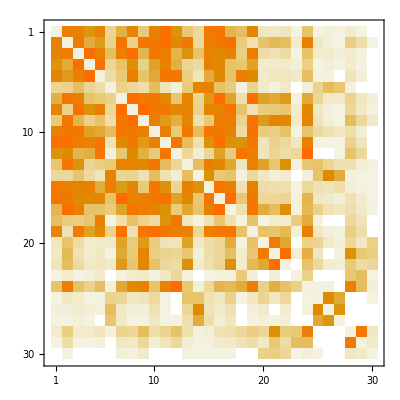

```mathematica
MatrixPlot[b]
```

```mathematica
(*Apply[distancefraction,allmemberlist ,{2}]*);
```

```mathematica
allmemberlist;
```

```mathematica
huskiesF⟦1⟧
```

{134.121,95.6584}

```mathematica
allmember[[1]]
```

Huskies_F1

# Sigma

```mathematica
xishu={{24.786753521652074,10.953743733097955,0.5949704993179812,0.5314529866839391,1.8545489137299482,1.2475945030181042,21.9541978168803,0.5715168333918333,9.53752600696458,5.0442099104373845,0.14528945383343764,6.66974192926631,0.04187770562770563,1.7892227534381553,2.0841564617828174,0.7125995359384064,0.511866058605189,0.29123048559599796,0.30690941877333977,4.932773793637368,6.516132337424632,6.789348535028153,7.550075846089328,8.634991249671202,4.64300137110585,7.922371278115284,2.183060503907335,0.45378246753246754,0.,1.3371566712463099},{10.953743733097955,123.43635196905888,2.781660810467276,4.12113501546063,7.622753082023881,15.610151699405233,72.03344450071276,2.9155817512334563,28.774717055567812,28.22093038372461,2.165073069964374,20.555997637394285,0.4931590909090909,3.505296355625941,3.403859232040567,0.7379234009297975,1.6088287625311226,3.9448034460464303,0.892063492063492,30.16113450312583,22.01183747143919,34.42212996070883,31.390192076886247,37.129280496560014,17.67752594829318,23.900522728642812,17.799996084165215,2.264473684210526,0.11827180310326377,12.496891665826963},{0.5949704993179812,2.781660810467276,2.067452395550281,0.4447154471544715,0.,0.,3.4483684426469954,0.07434717326021674,1.2110144242353647,0.4384361210275845,0.11854551344347261,1.6641668027108167,0.048791125541125545,0.,0.,0.,0.1378163878163878,0.,0.,2.134342529138731,0.7032398980870184,1.681061073274861,1.0540915026815973,0.9998544653158673,0.5717099567099567,0.3569076916637892,0.,0.,0.,0.2195710337483347},{0.5314529866839391,4.12113501546063,0.4447154471544715,14.045474374562456,0.2434450323339212,2.7145797239599676,13.30827780236421,1.2002351557907112,6.073464623593427,7.100333051775146,0.,2.8992011137213187,0.,0.271947323596499,0.9557516176414519,0.3239590375647893,0.33988014833245195,0.9203488098823764,0.19811165845648607,4.044940495491049,2.425733334137761,2.7713611680723362,3.383257622335295,6.434215604705068,0.3328046319102353,2.3131723318021375,2.9663565117952215,1.1316243259664311,0.2620380436971,0.8906376095307561},{1.8545489137299482,7.622753082023881,0.,0.2434450323339212,16.204577552920828,2.6516967473038875,7.481987296759158,0.2253750815394651,6.397363833501244,4.165065293070823,0.,3.0952242368382854,0.,0.,0.851683456103777,0.,0.9230007133939719,0.8690158761737024,0.6816792234135033,6.613930727651148,0.782367949532855,5.806434011810493,8.957154399876162,2.9124428251862327,0.6159857046266781,0.5890992346394182,8.162051686446189,0.20347402597402597,0.9303801863239552,1.9465992282882938},{1.2475945030181042,15.610151699405233,0.,2.7145797239599676,2.6516967473038875,23.047322935773146,16.631987786360725,0.15355673133450912,6.432859890022023,6.82170541750115,0.,2.845034498856283,0.,0.,0.409496442255063,0.,0.6996309483275776,1.1457159404899049,0.9766009852216748,8.312372021348125,3.9428140224275916,6.2664857394588065,8.357159638775212,7.3044319453032545,0.9622691892849093,4.03828092769592,9.703641276229561,1.670118762816131,0.2323511904761905,2.1642319283277134},{21.9541978168803,72.03344450071276,3.4483684426469954,13.30827780236421,7.481987296759158,16.631987786360725,248.35106468293782,8.828792863579029,70.96825771071846,40.12636608610648,2.166189322357168,30.14846305398012,0.6169090909090909,11.232647337575267,7.119284430996203,2.7734066218074744,1.7569568310652024,4.251906448533106,2.7817857819456293,53.437620895614614,38.86304815046418,55.90600773505638,53.18808115249453,52.02161639327983,29.070370852332353,38.367143340212536,24.800362790069837,3.349168850155692,2.324679466852697,24.257946415201843},{0.5715168333918333,2.9155817512334563,0.07434717326021674,1.2002351557907112,0.2253750815394651,0.15355673133450912,8.828792863579029,1.9921947517796537,4.09411712157692,1.0938440723828848,0.,0.5379171493798555,0.,0.,0.,0.,0.,0.03242210464432686,0.,1.8713045814585938,0.8991389814080031,1.7912713616736604,2.0063289782616263,0.9619411506368029,0.38705154998258445,0.,1.4282589612878804,0.,0.04525440313111545,0.2804051421539481},{9.53752600696458,28.774717055567812,1.2110144242353647,6.073464623593427,6.397363833501244,6.432859890022023,70.96825771071846,4.09411712157692,124.613079244757,16.370869118731882,0.28286531666930337,17.25018379572785,0.,5.521442881165137,7.091790504716707,1.4106385820225866,1.193605661032627,7.543167804458511,3.9189478673361733,32.6429575661125,25.848734698322534,34.28927408794842,31.007827086269046,35.92431409239718,20.401785995128417,19.654250204472095,9.659511659182066,5.567524350649349,1.3745278310459301,14.634768355196792},{5.0442099104373845,28.22093038372461,0.4384361210275845,7.100333051775146,4.165065293070823,6.82170541750115,40.12636608610648,1.0938440723828848,16.370869118731882,56.954446490325125,1.2119565217391304,11.736147583836827,0.,1.745060023854668,2.6523345099742466,0.4445595472555909,2.3557983929690614,1.4975449517421153,0.4050355774493706,15.148737204617202,9.20998086767254,15.862813180167594,17.220637342436355,16.83070033885259,5.638488896336943,16.26289822226829,13.956652933734947,1.6891555593529275,1.2994292237442922,4.918138411360741},{0.14528945383343764,2.165073069964374,0.11854551344347261,0.,0.,0.,2.166189322357168,0.,0.28286531666930337,1.2119565217391304,1.6609897917444192,0.15323722512260718,0.,0.38974673792671766,0.,0.,0.,0.,0.,0.22798013027604866,0.7840579710144929,1.378942558404136,1.4864988676870914,0.11277129899578879,0.,1.4625483493026465,0.,0.,0.,0.08641565153193059},{6.66974192926631,20.555997637394285,1.6641668027108167,2.8992011137213187,3.0952242368382854,2.845034498856283,30.14846305398012,0.5379171493798555,17.25018379572785,11.736147583836827,0.15323722512260718,55.47793326114056,0.7028300865800866,2.8526681709121284,3.5184880147309245,0.9645669848432994,0.8630563849285458,0.9326877145842662,2.3555313321397193,14.555624764037443,9.8021773828999,13.150775031137503,11.215487041101914,25.082515314740206,9.542136068521616,13.529824576755118,2.7805640780197907,0.,0.,4.60907131298204},{0.04187770562770563,0.4931590909090909,0.048791125541125545,0.,0.,0.,0.6169090909090909,0.,0.,0.,0.,0.7028300865800866,0.9192012987012987,0.,0.,0.,0.,0.,0.,0.46226623376623377,0.4438409090909091,0.5633106060606061,0.06678679653679653,0.,0.32968831168831164,0.,0.,0.,0.,0.2778138528138528},{1.7892227534381553,3.505296355625941,0.,0.271947323596499,0.,0.,11.232647337575267,0.,5.521442881165137,1.745060023854668,0.38974673792671766,2.8526681709121284,0.,7.238676623562558,0.6353209607820673,0.44241417497231444,0.03838383838383838,0.,0.8278061249487301,1.5247787719307277,1.930177913696235,4.236437571032136,0.7939209547374977,5.125575079748462,2.6931642594634257,7.499120849253156,0.,0.,0.,0.9955586823221689},{2.0841564617828174,3.403859232040567,0.,0.9557516176414519,0.851683456103777,0.409496442255063,7.119284430996203,0.,7.091790504716707,2.6523345099742466,0.,3.5184880147309245,0.,0.6353209607820673,11.361550470658063,0.08418235511258766,0.191005291005291,0.5160098522167487,1.7630131362889983,2.670776709748579,3.0157033566366818,2.9295505517318907,2.834282891918579,4.313535511788155,5.915723622855879,1.7865686051660545,0.6805239941328232,0.,0.01508480104370515,0.7502745219649178},{0.7125995359384064,0.7379234009297975,0.,0.3239590375647893,0.,0.,2.7734066218074744,0.,1.4106385820225866,0.4445595472555909,0.,0.9645669848432994,0.,0.44241417497231444,0.08418235511258766,1.4517861658177351,0.08994708994708994,0.,0.,0.7281542295995931,0.5219029961056538,0.905985906019652,0.054288083392561,0.9610843125128838,0.8728135092420806,2.517265871817367,0.,0.,0.,0.13268329554043837},{0.511866058605189,1.6088287625311226,0.1378163878163878,0.33988014833245195,0.9230007133939719,0.6996309483275776,1.7569568310652024,0.,1.193605661032627,2.3557983929690614,0.,0.8630563849285458,0.,0.03838383838383838,0.191005291005291,0.08994708994708994,4.059169278560525,0.,0.,1.127970333737062,0.5910604393213089,3.5216920336080006,3.326145741419422,0.7969693394693395,0.12997354497354496,2.8761508091942876,1.01729088639201,0.,0.4547752808988764,0.5008280939624223},{0.29123048559599796,3.9448034460464303,0.,0.9203488098823764,0.8690158761737024,1.1457159404899049,4.251906448533106,0.03242210464432686,7.543167804458511,1.4975449517421153,0.,0.9326877145842662,0.,0.,0.5160098522167487,0.,0.,5.813600668307117,0.16260262725779967,2.5278415390622078,2.120430283086707,2.3561445214266055,4.123931092701367,5.978831406400324,1.6506750836872541,1.5051000347589554,2.066075823854958,0.8574837662337662,0.,0.5787708589197155},{0.30690941877333977,0.892063492063492,0.,0.19811165845648607,0.6816792234135033,0.9766009852216748,2.7817857819456293,0.,3.9189478673361733,0.4050355774493706,0.,2.3555313321397193,0.,0.8278061249487301,1.7630131362889983,0.,0.,0.16260262725779967,6.665274622259364,0.7468842959472644,1.6691434044882323,1.7168060460899335,0.,3.570226534725168,1.9851529883984242,2.6417102956458276,0.,0.,0.,0.537352833853848},{4.932773793637368,30.16113450312583,2.134342529138731,4.044940495491049,6.613930727651148,8.312372021348125,53.437620895614614,1.8713045814585938,32.6429575661125,15.148737204617202,0.22798013027604866,14.555624764037443,0.46226623376623377,1.5247787719307277,2.670776709748579,0.7281542295995931,1.127970333737062,2.5278415390622078,0.7468842959472644,87.59620733691922,13.909988753037746,43.19231415000283,32.267815080351916,19.33418531152251,7.842309270197202,8.721953329424178,17.11004573111891,1.886114718614718,1.0608663524620463,13.275428784268547},{6.516132337424632,22.01183747143919,0.7032398980870184,2.425733334137761,0.782367949532855,3.9428140224275916,38.86304815046418,0.8991389814080031,25.848734698322534,9.20998086767254,0.7840579710144929,9.8021773828999,0.4438409090909091,1.930177913696235,3.0157033566366818,0.5219029961056538,0.5910604393213089,2.120430283086707,1.6691434044882323,13.909988753037746,45.3399940134085,8.402546285656651,11.84600136410253,29.289506721784605,14.316003617909363,20.021078830496254,0.28470695970695975,1.9661363636363631,0.,7.885159617557419},{6.789348535028153,34.42212996070883,1.681061073274861,2.7713611680723362,5.806434011810493,6.2664857394588065,55.90600773505638,1.7912713616736604,34.28927408794842,15.862813180167594,1.378942558404136,13.150775031137503,0.5633106060606061,4.236437571032136,2.9295505517318907,0.905985906019652,3.5216920336080006,2.3561445214266055,1.7168060460899335,43.19231415000283,8.402546285656651,109.62728296432053,33.32202538598132,7.876371011725153,7.822869494339577,13.866794398040645,19.535566462508406,0.,1.0800272104173798,17.174790413808317},{7.550075846089328,31.390192076886247,1.0540915026815973,3.383257622335295,8.957154399876162,8.357159638775212,53.18808115249453,2.0063289782616263,31.007827086269046,17.220637342436355,1.4864988676870914,11.215487041101914,0.06678679653679653,0.7939209547374977,2.834282891918579,0.054288083392561,3.326145741419422,4.123931092701367,0.,32.267815080351916,11.84600136410253,33.32202538598132,82.60254738717005,8.728566480052173,5.065521580148482,5.97565352216326,17.193562941397257,0.,1.5868095661344896,9.961944057697085},{8.634991249671202,37.129280496560014,0.9998544653158673,6.434215604705068,2.9124428251862327,7.3044319453032545,52.02161639327983,0.9619411506368029,35.92431409239718,16.83070033885259,0.11277129899578879,25.082515314740206,0.,5.125575079748462,4.313535511788155,0.9610843125128838,0.7969693394693395,5.978831406400324,3.570226534725168,19.33418531152251,29.289506721784605,7.876371011725153,8.728566480052173,105.9772401198176,16.172159744301446,22.77061373011734,1.7454582316996505,2.75849756968178,0.,10.883248355976686},{4.64300137110585,17.67752594829318,0.5717099567099567,0.3328046319102353,0.6159857046266781,0.9622691892849093,29.070370852332353,0.38705154998258445,20.401785995128417,5.638488896336943,0.,9.542136068521616,0.32968831168831164,2.6931642594634257,5.915723622855879,0.8728135092420806,0.12997354497354496,1.6506750836872541,1.9851529883984242,7.842309270197202,14.316003617909363,7.822869494339577,5.065521580148482,16.172159744301446,42.10446002200209,12.479137494925265,0.6625986026594546,0.,0.,6.4808789645843525},{7.922371278115284,23.900522728642812,0.3569076916637892,2.3131723318021375,0.5890992346394182,4.03828092769592,38.367143340212536,0.,19.654250204472095,16.26289822226829,1.4625483493026465,13.529824576755118,0.,7.499120849253156,1.7865686051660545,2.517265871817367,2.8761508091942876,1.5051000347589554,2.6417102956458276,8.721953329424178,20.021078830496254,13.866794398040645,5.97565352216326,22.77061373011734,12.479137494925265,73.4421009753434,0.,2.0511931818181814,0.,7.134335630294305},{2.183060503907335,17.799996084165215,0.,2.9663565117952215,8.162051686446189,9.703641276229561,24.800362790069837,1.4282589612878804,9.659511659182066,13.956652933734947,0.,2.7805640780197907,0.,0.,0.6805239941328232,0.,1.01729088639201,2.066075823854958,0.,17.11004573111891,0.28470695970695975,19.535566462508406,17.193562941397257,1.7454582316996505,0.6625986026594546,0.,43.485063905498336,0.7770467836257309,0.8792842495953226,7.001750330941375},{0.45378246753246754,2.264473684210526,0.,1.1316243259664311,0.20347402597402597,1.670118762816131,3.349168850155692,0.,5.567524350649349,1.6891555593529275,0.,0.,0.,0.,0.,0.,0.,0.8574837662337662,0.,1.886114718614718,1.9661363636363631,0.,0.,2.75849756968178,0.,2.0511931818181814,0.7770467836257309,7.207757082099187,0.,1.656386230728336},{0.,0.11827180310326377,0.,0.2620380436971,0.9303801863239552,0.2323511904761905,2.324679466852697,0.04525440313111545,1.3745278310459301,1.2994292237442922,0.,0.,0.,0.,0.01508480104370515,0.,0.4547752808988764,0.,0.,1.0608663524620463,0.,1.0800272104173798,1.5868095661344896,0.,0.,0.,0.8792842495953226,0.,0.571763343584526,0.3216124704075874},{1.3371566712463099,12.496891665826963,0.2195710337483347,0.8906376095307561,1.9465992282882938,2.1642319283277134,24.257946415201843,0.2804051421539481,14.634768355196792,4.918138411360741,0.08641565153193059,4.60907131298204,0.2778138528138528,0.9955586823221689,0.7502745219649178,0.13268329554043837,0.5008280939624223,0.5787708589197155,0.537352833853848,13.275428784268547,7.885159617557419,17.174790413808317,9.961944057697085,10.883248355976686,6.4808789645843525,7.134335630294305,7.001750330941375,1.656386230728336,0.3216124704075874,16.223918154277925}};
```

```mathematica
sigma[{member1_,member2_}]:=distancefraction[member1,member2]*fractionmyteam[member1]*fractionmyteam[member2]
```

```mathematica
distancefraction["Huskies_F1","Huskies_G1"]
```

distancefraction[Huskies_F1,Huskies_G1]

```mathematica
sigma[{member1_,member2_}]:=fractionmyteam[member1]*fractionmyteam[member2]
```

```mathematica
fractionmyteam["Huskies_F1"]
```

253/327

```mathematica
fractionmyteam["Huskies_M1"]
```

1327/3566

```mathematica
huskiesD⟦8⟧
```

{108.63,174.76}

```mathematica
distancefraction["Huskies_M1","Huskies_M3"]
```

distancefraction[Huskies_M1,Huskies_M3]

```mathematica
sigma[{"Huskies_F1","Huskies_F2"}]
```

299299/935547

```mathematica
test03=allmemberlist;
```

```mathematica
test03;
```

```mathematica
sigma[{"Huskies_F1","Huskies_F2"}]
```

299299/935547

```mathematica
veryimportantlist=ParallelMap[sigma,test03,{2}]
```

(64009/106929 | 299299/935547 | 33143/82077 | 203159/361662 | 153571/295281 | 159137/344331 | 335731/1166082 | 24035/77172 | 77924/268467 | 235543/625551 | 17963/49704 | 25507/62457 | 1771/6649 | 4114/10137 | 92345/209934 | 28589/62784 | 3795/11336 | 161/327 | 9108/25615 | 64009/173310 | 203665/575193 | 78683/229118 | 204677/639939 | 291709/728556 | 58190/138321 | 257048/581079 | 152812/360681 | 13156/47415 | 17963/43491 | 126247/229881
299299/935547 | 1399489/8185321 | 154973/718111 | 135707/452038 | 102583/369069 | 57239/231741 | 1569841/10202326 | 112385/675196 | 364364/2348881 | 1101373/5473093 | 83993/434872 | 1311947/6010961 | 24843/174521 | 442442/2039893 | 431795/1836762 | 133679/549312 | 4095/22888 | 8281/31471 | 127764/672335 | 299299/1516330 | 952315/5032499 | 1103739/6013822 | 957047/5598977 | 1363999/6374308 | 272090/1210203 | 1201928/5083997 | 714532/3155683 | 61516/414845 | 11999/54359 | 590317/2011283
33143/82077 | 154973/718111 | 17161/63001 | 105193/277606 | 79517/226653 | 82399/264303 | 173837/895066 | 12445/59236 | 40348/206071 | 121961/480163 | 9301/38152 | 145279/527351 | 2751/15311 | 48994/178963 | 47815/161142 | 14803/48192 | 5895/26104 | 917/2761 | 14148/58985 | 33143/133030 | 105455/441509 | 122223/527602 | 105979/491207 | 151043/559228 | 30130/106173 | 133096/446027 | 79124/276853 | 6812/36395 | 9301/33383 | 65369/176453
203159/361662 | 135707/452038 | 105193/277606 | 644809/1223236 | 487421/998718 | 505087/1164618 | 1065581/3943996 | 76285/261016 | 17666/64859 | 106799/302254 | 57013/168112 | 80957/211246 | 2409/9638 | 150161/394289 | 293095/710052 | 90739/212352 | 36135/115024 | 73/158 | 43362/129955 | 203159/586180 | 92345/277922 | 749199/2324812 | 649627/2164442 | 925859/2464168 | 92345/233919 | 407924/982681 | 242506/609959 | 20878/80185 | 57013/147098 | 400697/777518
153571/295281 | 102583/369069 | 79517/226653 | 487421/998718 | 368449/815409 | 381803/950859 | 805489/3220098 | 57665/213108 | 26708/105909 | 80731/246777 | 43097/137256 | 673163/1897203 | 607/2623 | 227018/643839 | 221555/579726 | 68591/173376 | 9105/31304 | 607/1419 | 21852/70735 | 153571/478590 | 69805/226911 | 188777/632702 | 491063/1767171 | 699871/2011884 | 139610/381969 | 616712/1604631 | 366628/996009 | 31564/130935 | 43097/120099 | 302893/634809
159137/344331 | 57239/231741 | 82399/264303 | 505087/1164618 | 381803/950859 | 395641/1108809 | 834683/3754998 | 59755/248508 | 193732/864513 | 585599/2014389 | 44659/160056 | 697561/2212353 | 4403/21411 | 235246/750789 | 229585/676026 | 71077/202176 | 3145/12168 | 4403/11583 | 2516/9165 | 159137/558090 | 506345/1852227 | 195619/737802 | 508861/2060721 | 725237/2346084 | 144670/445419 | 639064/1871181 | 379916/1161459 | 2516/11745 | 44659/140049 | 8483/20007
335731/1166082 | 1569841/10202326 | 173837/895066 | 1065581/3943996 | 805489/3220098 | 834683/3754998 | 1760929/12716356 | 126065/841576 | 204358/1463843 | 1235437/6821758 | 94217/542032 | 1471643/7492166 | 27867/217526 | 248149/1271279 | 484355/2289372 | 149951/684672 | 59715/370864 | 9289/39226 | 71658/419005 | 335731/1889980 | 1068235/6272594 | 1238091/7495732 | 1073543/6978662 | 1530031/7945048 | 152605/754209 | 674116/3168391 | 400754/1966649 | 34502/258535 | 94217/474278 | 662173/2506898
24035/77172 | 112385/675196 | 12445/59236 | 76285/261016 | 57665/213108 | 59755/248508 | 126065/841576 | 9025/55696 | 7315/48439 | 88445/451468 | 355/1888 | 105355/495836 | 1995/14396 | 17765/84134 | 34675/151512 | 10735/45312 | 4275/24544 | 665/2596 | 513/2773 | 4807/25016 | 76475/415124 | 88635/496072 | 4045/24308 | 109535/525808 | 10925/49914 | 24130/104843 | 14345/65077 | 247/1711 | 355/1652 | 2495/8732
77924/268467 | 364364/2348881 | 40348/206071 | 17666/64859 | 26708/105909 | 193732/864513 | 204358/1463843 | 7315/48439 | 94864/674041 | 286748/1570573 | 5467/31198 | 31052/156811 | 6468/50081 | 115192/585373 | 56210/263541 | 8701/39408 | 3465/21346 | 196/821 | 33264/192935 | 38962/217565 | 247940/1444139 | 143682/862871 | 249172/1606697 | 88781/457297 | 70840/347283 | 312928/1458917 | 186032/905563 | 16016/119045 | 3124/15599 | 153692/577163
235543/625551 | 1101373/5473093 | 121961/480163 | 106799/302254 | 80731/246777 | 585599/2014389 | 1235437/6821758 | 88445/451468 | 286748/1570573 | 866761/3659569 | 3479/15304 | 1032479/4019213 | 19551/116693 | 348194/1363969 | 339815/1228146 | 105203/367296 | 41895/198952 | 6517/21043 | 100548/449555 | 235543/1013890 | 749455/3364967 | 868623/4021126 | 39641/197039 | 1073443/4262164 | 214130/809199 | 945896/3399401 | 562324/2110039 | 48412/277385 | 497/1913 | 24451/70781
17963/49704 | 83993/434872 | 9301/38152 | 57013/168112 | 43097/137256 | 44659/160056 | 94217/542032 | 355/1888 | 5467/31198 | 3479/15304 | 5041/23104 | 78739/319352 | 1491/9272 | 13277/54188 | 25915/97584 | 8023/29184 | 3195/15808 | 497/1672 | 1917/8930 | 17963/80560 | 57155/267368 | 66243/319504 | 57439/297464 | 81863/338656 | 8165/32148 | 9017/33763 | 10721/41914 | 923/5510 | 5041/20216 | 35429/106856
25507/62457 | 1311947/6010961 | 145279/527351 | 80957/211246 | 673163/1897203 | 697561/2212353 | 1471643/7492166 | 105355/495836 | 31052/156811 | 1032479/4019213 | 78739/319352 | 1229881/4414201 | 23289/128161 | 37706/136183 | 404785/1348842 | 125317/403392 | 49905/218504 | 7763/23111 | 119772/493735 | 25507/101230 | 892745/3695659 | 1034697/4416302 | 897181/4111657 | 1278677/4681028 | 255070/888723 | 1126744/3733477 | 669836/2317403 | 57668/304645 | 78739/279433 | 553391/1477003
1771/6649 | 24843/174521 | 2751/15311 | 2409/9638 | 607/2623 | 4403/21411 | 27867/217526 | 1995/14396 | 6468/50081 | 19551/116693 | 1491/9272 | 23289/128161 | 441/3721 | 7854/43493 | 2555/13054 | 791/3904 | 945/6344 | 147/671 | 2268/14335 | 5313/32330 | 16905/107299 | 19593/128222 | 16989/119377 | 24213/135908 | 1610/8601 | 21336/108397 | 12684/67283 | 1092/8845 | 213/1159 | 10479/42883
4114/10137 | 442442/2039893 | 48994/178963 | 150161/394289 | 227018/643839 | 235246/750789 | 248149/1271279 | 17765/84134 | 115192/585373 | 348194/1363969 | 13277/54188 | 37706/136183 | 7854/43493 | 139876/508369 | 68255/228873 | 21131/68448 | 8415/37076 | 238/713 | 40392/167555 | 2057/8215 | 13090/54529 | 174471/749363 | 302566/1395341 | 215611/794282 | 3740/13113 | 379984/1267001 | 225896/786439 | 19448/103385 | 26554/94829 | 186626/501239
92345/209934 | 431795/1836762 | 47815/161142 | 293095/710052 | 221555/579726 | 229585/676026 | 484355/2289372 | 34675/151512 | 56210/263541 | 339815/1228146 | 25915/97584 | 404785/1348842 | 2555/13054 | 68255/228873 | 133225/412164 | 41245/123264 | 5475/22256 | 2555/7062 | 1314/5029 | 18469/68052 | 293825/1129278 | 113515/449828 | 295285/1256394 | 420845/1430376 | 41975/135783 | 185420/570417 | 110230/354063 | 1898/9309 | 25915/85386 | 182135/451326
28589/62784 | 133679/549312 | 14803/48192 | 90739/212352 | 68591/173376 | 71077/202176 | 149951/684672 | 10735/45312 | 8701/39408 | 105203/367296 | 8023/29184 | 125317/403392 | 791/3904 | 21131/68448 | 41245/123264 | 12769/36864 | 1695/6656 | 791/2112 | 1017/3760 | 28589/101760 | 90965/337728 | 35143/134528 | 91417/375744 | 130289/427776 | 12995/40608 | 14351/42648 | 17063/52944 | 1469/6960 | 8023/25536 | 56387/134976
3795/11336 | 4095/22888 | 5895/26104 | 36135/115024 | 9105/31304 | 3145/12168 | 59715/370864 | 4275/24544 | 3465/21346 | 41895/198952 | 3195/15808 | 49905/218504 | 945/6344 | 8415/37076 | 5475/22256 | 1695/6656 | 2025/10816 | 315/1144 | 243/1222 | 2277/11024 | 36225/182936 | 41985/218608 | 36405/203528 | 51885/231712 | 575/2444 | 5715/23101 | 6795/28678 | 9/58 | 3195/13832 | 22455/73112
161/327 | 8281/31471 | 917/2761 | 73/158 | 607/1419 | 4403/11583 | 9289/39226 | 665/2596 | 196/821 | 6517/21043 | 497/1672 | 7763/23111 | 147/671 | 238/713 | 2555/7062 | 791/2112 | 315/1144 | 49/121 | 756/2585 | 161/530 | 5635/19349 | 6531/23122 | 5663/21527 | 8071/24508 | 1610/4653 | 7112/19547 | 4228/12133 | 364/1595 | 71/209 | 3493/7733
9108/25615 | 127764/672335 | 14148/58985 | 43362/129955 | 21852/70735 | 2516/9165 | 71658/419005 | 513/2773 | 33264/192935 | 100548/449555 | 1917/8930 | 119772/493735 | 2268/14335 | 40392/167555 | 1314/5029 | 1017/3760 | 243/1222 | 756/2585 | 11664/55225 | 13662/62275 | 17388/82673 | 50382/246985 | 87372/459895 | 31131/130895 | 552/2209 | 109728/417595 | 65232/259205 | 5616/34075 | 7668/31255 | 53892/165205
64009/173310 | 299299/1516330 | 33143/133030 | 203159/586180 | 153571/478590 | 159137/558090 | 335731/1889980 | 4807/25016 | 38962/217565 | 235543/1013890 | 17963/80560 | 25507/101230 | 5313/32330 | 2057/8215 | 18469/68052 | 28589/101760 | 2277/11024 | 161/530 | 13662/62275 | 64009/280900 | 40733/186454 | 236049/1114060 | 204677/1037210 | 291709/1180840 | 5819/22419 | 128524/470905 | 76406/292295 | 6578/38425 | 17963/70490 | 126247/372590
203665/575193 | 952315/5032499 | 105455/441509 | 92345/277922 | 69805/226911 | 506345/1852227 | 1068235/6272594 | 76475/415124 | 247940/1444139 | 749455/3364967 | 57155/267368 | 892745/3695659 | 16905/107299 | 13090/54529 | 293825/1129278 | 90965/337728 | 36225/182936 | 5635/19349 | 17388/82673 | 40733/186454 | 648025/3094081 | 751065/3697418 | 651245/3442363 | 928165/3919052 | 185150/744057 | 817880/3125743 | 486220/1940177 | 8372/51011 | 8165/33421 | 401695/1236577
78683/229118 | 1103739/6013822 | 122223/527602 | 749199/2324812 | 188777/632702 | 195619/737802 | 1238091/7495732 | 88635/496072 | 143682/862871 | 868623/4021126 | 66243/319504 | 1034697/4416302 | 19593/128222 | 174471/749363 | 113515/449828 | 35143/134528 | 41985/218608 | 6531/23122 | 50382/246985 | 236049/1114060 | 751065/3697418 | 870489/4418404 | 754797/4113614 | 1075749/4683256 | 35765/148191 | 473964/1867627 | 281766/1159253 | 24258/152395 | 66243/279566 | 465567/1477706
204677/639939 | 957047/5598977 | 105979/491207 | 649627/2164442 | 491063/1767171 | 508861/2060721 | 1073543/6978662 | 4045/24308 | 249172/1606697 | 39641/197039 | 57439/297464 | 897181/4111657 | 16989/119377 | 302566/1395341 | 295285/1256394 | 91417/375744 | 36405/203528 | 5663/21527 | 87372/459895 | 204677/1037210 | 651245/3442363 | 754797/4113614 | 654481/3829849 | 932777/4360196 | 186070/827811 | 821944/3477589 | 488636/2158571 | 42068/283765 | 57439/260281 | 403691/1375771
291709/728556 | 1363999/6374308 | 151043/559228 | 925859/2464168 | 699871/2011884 | 725237/2346084 | 1530031/7945048 | 109535/525808 | 88781/457297 | 1073443/4262164 | 81863/338656 | 1278677/4681028 | 24213/135908 | 215611/794282 | 420845/1430376 | 130289/427776 | 51885/231712 | 8071/24508 | 31131/130895 | 291709/1180840 | 928165/3919052 | 1075749/4683256 | 932777/4360196 | 1329409/4963984 | 132595/471222 | 292862/989789 | 174103/614371 | 14989/80765 | 81863/296324 | 575347/1566284
58190/138321 | 272090/1210203 | 30130/106173 | 92345/233919 | 139610/381969 | 144670/445419 | 152605/754209 | 10925/49914 | 70840/347283 | 214130/809199 | 8165/32148 | 255070/888723 | 1610/8601 | 3740/13113 | 41975/135783 | 12995/40608 | 575/2444 | 1610/4653 | 552/2209 | 5819/22419 | 185150/744057 | 35765/148191 | 186070/827811 | 132595/471222 | 52900/178929 | 233680/751671 | 138920/466569 | 2392/12267 | 16330/56259 | 114770/297369
257048/581079 | 1201928/5083997 | 133096/446027 | 407924/982681 | 616712/1604631 | 639064/1871181 | 674116/3168391 | 24130/104843 | 312928/1458917 | 945896/3399401 | 9017/33763 | 1126744/3733477 | 21336/108397 | 379984/1267001 | 185420/570417 | 14351/42648 | 5715/23101 | 7112/19547 | 109728/417595 | 128524/470905 | 817880/3125743 | 473964/1867627 | 821944/3477589 | 292862/989789 | 233680/751671 | 1032256/3157729 | 613664/1960031 | 52832/257665 | 72136/236341 | 506984/1249231
152812/360681 | 714532/3155683 | 79124/276853 | 242506/609959 | 366628/996009 | 379916/1161459 | 400754/1966649 | 14345/65077 | 186032/905563 | 562324/2110039 | 10721/41914 | 669836/2317403 | 12684/67283 | 225896/786439 | 110230/354063 | 17063/52944 | 6795/28678 | 4228/12133 | 65232/259205 | 76406/292295 | 486220/1940177 | 281766/1159253 | 488636/2158571 | 174103/614371 | 138920/466569 | 613664/1960031 | 364816/1216609 | 31408/159935 | 42884/146699 | 301396/775409
13156/47415 | 61516/414845 | 6812/36395 | 20878/80185 | 31564/130935 | 2516/11745 | 34502/258535 | 247/1711 | 16016/119045 | 48412/277385 | 923/5510 | 57668/304645 | 1092/8845 | 19448/103385 | 1898/9309 | 1469/6960 | 9/58 | 364/1595 | 5616/34075 | 6578/38425 | 8372/51011 | 24258/152395 | 42068/283765 | 14989/80765 | 2392/12267 | 52832/257665 | 31408/159935 | 2704/21025 | 3692/19285 | 25948/101935
17963/43491 | 11999/54359 | 9301/33383 | 57013/147098 | 43097/120099 | 44659/140049 | 94217/474278 | 355/1652 | 3124/15599 | 497/1913 | 5041/20216 | 78739/279433 | 213/1159 | 26554/94829 | 25915/85386 | 8023/25536 | 3195/13832 | 71/209 | 7668/31255 | 17963/70490 | 8165/33421 | 66243/279566 | 57439/260281 | 81863/296324 | 16330/56259 | 72136/236341 | 42884/146699 | 3692/19285 | 5041/17689 | 35429/93499
126247/229881 | 590317/2011283 | 65369/176453 | 400697/777518 | 302893/634809 | 8483/20007 | 662173/2506898 | 2495/8732 | 153692/577163 | 24451/70781 | 35429/106856 | 553391/1477003 | 10479/42883 | 186626/501239 | 182135/451326 | 56387/134976 | 22455/73112 | 3493/7733 | 53892/165205 | 126247/372590 | 401695/1236577 | 465567/1477706 | 403691/1375771 | 575347/1566284 | 114770/297369 | 506984/1249231 | 301396/775409 | 25948/101935 | 35429/93499 | 249001/494209)

```mathematica
Out[406]*1000//N
```

1000. Null

```mathematica
realmatrix=veryimportantlist*b*xishu
```

(0.00284382 | 0.100411 | 0.00665382 | 0.00637985 | 0.0267127 | 0.00276278 | 0.0908613 | 0.00504908 | 0.0214886 | 0.0544226 | 0.00187689 | 0.0584713 | 0.0000919287 | 0.00313141 | 0.0298708 | 0.0108214 | 0.00211839 | 0.00144282 | 0.00288639 | 0.00331719 | 0.00331659 | 0.00513908 | 0.000231414 | 0.030482 | 0.000187183 | 0.00134339 | 0.0000886355 | 0.000132726 | 0. | 0.
0.100411 | 0.00404496 | 0.0185239 | 0.0187331 | 0.0412177 | 0.0199525 | 0.366452 | 0.00274387 | 0.148858 | 0.181228 | 0.0149476 | 0.116517 | 0.00228734 | 0.00327864 | 0.0230818 | 0.00559302 | 0.010289 | 0.00765942 | 0.000487357 | 0.0524873 | 0.046304 | 0.0635697 | 0.00565612 | 0.229177 | 0.00571314 | 0.00216595 | 0.000386239 | 0.0020273 | 0.000087565 | 0.000351497
0.00665382 | 0.0185239 | 0.000107936 | 0.00603976 | 0. | 0. | 0.0193186 | 0.000559826 | 0.00293124 | 0.00355378 | 0.000891786 | 0.00566757 | 0.000188184 | 0. | 0. | 0. | 0.000891777 | 0. | 0. | 0.00183449 | 0.000482903 | 0.00145547 | 0.0000217942 | 0.00240679 | 0.000171026 | 0.000112269 | 0. | 0. | 0. | 0.
0.00637985 | 0.0187331 | 0.00603976 | 0.00141904 | 0.00429251 | 0.00564109 | 0.0320452 | 0.00769806 | 0.00951181 | 0.0432767 | 0. | 0.0159714 | 0. | 0.000406929 | 0.0113043 | 0.00362158 | 0.000951603 | 0.00350449 | 0.00114027 | 0.00147781 | 0.000772398 | 0.00102705 | 0.000389243 | 0.0139005 | 0.0000125906 | 0.0004601 | 0.000113019 | 0.000310598 | 9.73283×10^-6 | 0.
0.0267127 | 0.0412177 | 0. | 0.00429251 | 0.00140339 | 0.00367331 | 0.0145278 | 0.00175911 | 0.0143781 | 0.0216757 | 0. | 0.0357837 | 0. | 0. | 0.00492835 | 0. | 0.00239261 | 0.0107228 | 0.00546907 | 0.00244059 | 0.000415166 | 0.00315443 | 0.00286232 | 0.0101946 | 0.0000431516 | 0.0000433944 | 0. | 0.000108114 | 0.000127978 | 0.
0.00276278 | 0.0199525 | 0. | 0.00564109 | 0.00367331 | 0.00157617 | 0.0212576 | 0.000162768 | 0.00483515 | 0.0201448 | 0. | 0.000343861 | 0. | 0. | 0.00401148 | 0. | 0.00133435 | 0.0000417361 | 0.00138738 | 0.00272572 | 0.000206584 | 0.00191066 | 0. | 0.000865546 | 0.00161736 | 0.01401 | 0.0261592 | 0.000102857 | 0. | 0.
0.0908613 | 0.366452 | 0.0193186 | 0.0320452 | 0.0145278 | 0.0212576 | 0.00659148 | 0.0477806 | 0.316164 | 0.231903 | 0.00977862 | 0.0488052 | 0.0021888 | 0.0105059 | 0.0293013 | 0.0227596 | 0.00474434 | 0.00328069 | 0.0171877 | 0.163742 | 0.105286 | 0.179639 | 0.00156819 | 0.159369 | 0.0276205 | 0.0117342 | 0.00581163 | 0.00231293 | 0.000840854 | 0.00245616
0.00504908 | 0.00274387 | 0.000559826 | 0.00769806 | 0.00175911 | 0.000162768 | 0.0477806 | 0.0000618718 | 0.0231667 | 0.00683838 | 0. | 0.00296831 | 0. | 0. | 0. | 0. | 0. | 0.0000740199 | 0. | 0.00265338 | 0.00128576 | 0.00263772 | 0.000351942 | 0.00520417 | 0.000146133 | 0. | 0.0000301708 | 0. | 0.0000139791 | 0.0000153561
0.0214886 | 0.148858 | 0.00293124 | 0.00951181 | 0.0143781 | 0.00483515 | 0.316164 | 0.0231667 | 0.00336137 | 0.086216 | 0.000964285 | 0.0491027 | 0. | 0.00322784 | 0.0117412 | 0.0089841 | 0.00597876 | 0.00931897 | 0.022533 | 0.113722 | 0.125886 | 0.149377 | 0.00553 | 0.197838 | 0.00917273 | 0.00161599 | 0.000190165 | 0.00760884 | 0.0011871 | 0.00448154
0.0544226 | 0.181228 | 0.00355378 | 0.0432767 | 0.0216757 | 0.0201448 | 0.231903 | 0.00683838 | 0.086216 | 0.00258544 | 0.00789433 | 0.0234023 | 0. | 0.00452523 | 0.0234192 | 0.00396582 | 0.0137391 | 0.00173337 | 0.00323817 | 0.0259689 | 0.0123843 | 0.030539 | 0.000664017 | 0.037372 | 0.00586241 | 0.0130097 | 0.0064159 | 0.000988816 | 0.000194112 | 0.
0.00187689 | 0.0149476 | 0.000891786 | 0. | 0. | 0. | 0.00977862 | 0. | 0.000964285 | 0.00789433 | 0.0000694599 | 0.00126 | 0. | 0.000283693 | 0. | 0. | 0. | 0. | 0. | 0.000121788 | 0.00086735 | 0.00123291 | 0.000522635 | 0.000781099 | 0. | 0.0000374316 | 0. | 0. | 0. | 0.
0.0584713 | 0.116517 | 0.00566757 | 0.0159714 | 0.0357837 | 0.000343861 | 0.0488052 | 0.00296831 | 0.0491027 | 0.0234023 | 0.00126 | 0.00296257 | 0.000563003 | 0.000454148 | 0.00505938 | 0.00516886 | 0.00145453 | 0.010448 | 0.0164825 | 0.00808382 | 0.0111189 | 0.0106296 | 0.0107881 | 0.256729 | 0. | 0. | 0.0000770207 | 0. | 0. | 0.
0.0000919287 | 0.00228734 | 0.000188184 | 0. | 0. | 0. | 0.0021888 | 0. | 0. | 0. | 0. | 0.000563003 | 0.0000208798 | 0. | 0. | 0. | 0. | 0. | 0. | 0.00131041 | 0.000576306 | 0.00188899 | 1.82169×10^-6 | 0. | 0.000544096 | 0. | 0. | 0. | 0. | 0.0000130115
0.00313141 | 0.00327864 | 0. | 0.000406929 | 0. | 0. | 0.0105059 | 0. | 0.00322784 | 0.00452523 | 0.000283693 | 0.000454148 | 0. | 0.000381734 | 0.00415792 | 0.00108636 | 0.0000768077 | 0. | 0.000860571 | 0.000658588 | 0.000177614 | 0.00103976 | 0. | 0.000533343 | 0.00677217 | 0.0584084 | 0. | 0. | 0. | 0.0000355224
0.0298708 | 0.0230818 | 0. | 0.0113043 | 0.00492835 | 0.00401148 | 0.0293013 | 0. | 0.0117412 | 0.0234192 | 0. | 0.00505938 | 0. | 0.00415792 | 0.000703867 | 0.000939383 | 0.00134636 | 0.000536723 | 0.0132875 | 0.00250063 | 0.0026318 | 0.00240876 | 0.0000638361 | 0.005473 | 0.00525753 | 0.00139133 | 0.000710621 | 0. | 8.77489×10^-7 | 0.0000290155
0.0108214 | 0.00559302 | 0. | 0.00362158 | 0. | 0. | 0.0227596 | 0. | 0.0089841 | 0.00396582 | 0. | 0.00516886 | 0. | 0.00108636 | 0.000939383 | 0.0000963817 | 0.000858278 | 0. | 0. | 0.000901801 | 0.000619673 | 0.00113403 | 2.53149×10^-6 | 0.00361868 | 0.000481799 | 0.000974095 | 0. | 0. | 0. | 5.31186×10^-6
0.00211839 | 0.010289 | 0.000891777 | 0.000951603 | 0.00239261 | 0.00133435 | 0.00474434 | 0. | 0.00597876 | 0.0137391 | 0. | 0.00145453 | 0. | 0.0000768077 | 0.00134636 | 0.000858278 | 0.000145658 | 0. | 0. | 0.00352766 | 0.00117771 | 0.014843 | 0.000114029 | 0.00198381 | 0.000175825 | 0.00204562 | 0.000438881 | 0. | 0.000120801 | 0.0000294816
0.00144282 | 0.00765942 | 0. | 0.00350449 | 0.0107228 | 0.0000417361 | 0.00328069 | 0.0000740199 | 0.00931897 | 0.00173337 | 0. | 0.010448 | 0. | 0. | 0.000536723 | 0. | 0. | 0.000451225 | 0.000423818 | 0.0000735881 | 0.000650968 | 0.000701546 | 0.00800521 | 0.0298126 | 0.0000547346 | 0. | 0. | 0.000843892 | 0. | 0.
0.00288639 | 0.000487357 | 0. | 0.00114027 | 0.00546907 | 0.00138738 | 0.0171877 | 0. | 0.022533 | 0.00323817 | 0. | 0.0164825 | 0. | 0.000860571 | 0.0132875 | 0. | 0. | 0.000423818 | 0.000269816 | 0.00146031 | 0.00289325 | 0.00389306 | 0. | 0.0243301 | 0.000855692 | 0.000266082 | 0. | 0. | 0. | 0.
0.00331719 | 0.0524873 | 0.00183449 | 0.00147781 | 0.00244059 | 0.00272572 | 0.163742 | 0.00265338 | 0.113722 | 0.0259689 | 0.000121788 | 0.00808382 | 0.00131041 | 0.000658588 | 0.00250063 | 0.000901801 | 0.00352766 | 0.0000735881 | 0.00146031 | 0.00382571 | 0.0937702 | 0.147339 | 0. | 0.0274627 | 0.00975335 | 0.0027375 | 0.00171445 | 0.00142336 | 0.000388607 | 0.0258641
0.00331659 | 0.046304 | 0.000482903 | 0.000772398 | 0.000415166 | 0.000206584 | 0.105286 | 0.00128576 | 0.125886 | 0.0123843 | 0.00086735 | 0.0111189 | 0.000576306 | 0.000177614 | 0.0026318 | 0.000619673 | 0.00117771 | 0.000650968 | 0.00289325 | 0.0937702 | 0.00182003 | 0.061665 | 0.00107383 | 0.0997137 | 0.00648635 | 0. | 0.000013675 | 0.00708145 | 0. | 0.0154644
0.00513908 | 0.0635697 | 0.00145547 | 0.00102705 | 0.00315443 | 0.00191066 | 0.179639 | 0.00263772 | 0.149377 | 0.030539 | 0.00123291 | 0.0106296 | 0.00188899 | 0.00103976 | 0.00240876 | 0.00113403 | 0.014843 | 0.000701546 | 0.00389306 | 0.147339 | 0.061665 | 0.00413956 | 0. | 0.0161243 | 0.00814184 | 0.00370964 | 0.00227517 | 0. | 0.000882877 | 0.0238534
0.000231414 | 0.00565612 | 0.0000217942 | 0.000389243 | 0.00286232 | 0. | 0.00156819 | 0.000351942 | 0.00553 | 0.000664017 | 0.000522635 | 0.0107881 | 1.82169×10^-6 | 0. | 0.0000638361 | 2.53149×10^-6 | 0.000114029 | 0.00800521 | 0. | 0. | 0.00107383 | 0. | 0.00270549 | 0.0107368 | 0. | 0. | 0. | 0. | 0.0035236 | 0.000280127
0.030482 | 0.229177 | 0.00240679 | 0.0139005 | 0.0101946 | 0.000865546 | 0.159369 | 0.00520417 | 0.197838 | 0.037372 | 0.000781099 | 0.256729 | 0. | 0.000533343 | 0.005473 | 0.00361868 | 0.00198381 | 0.0298126 | 0.0243301 | 0.0274627 | 0.0997137 | 0.0161243 | 0.0107368 | 0.00543974 | 0.000436091 | 0.00193697 | 0. | 0.014669 | 0. | 0.00191556
0.000187183 | 0.00571314 | 0.000171026 | 0.0000125906 | 0.0000431516 | 0.00161736 | 0.0276205 | 0.000146133 | 0.00917273 | 0.00586241 | 0. | 0. | 0.000544096 | 0.00677217 | 0.00525753 | 0.000481799 | 0.000175825 | 0.0000547346 | 0.000855692 | 0.00975335 | 0.00648635 | 0.00814184 | 0. | 0.000436091 | 0.00238584 | 0.100752 | 0.00313845 | 0. | 0. | 0.000239703
0.00134339 | 0.00216595 | 0.000112269 | 0.0004601 | 0.0000433944 | 0.01401 | 0.0117342 | 0. | 0.00161599 | 0.0130097 | 0.0000374316 | 0. | 0. | 0.0584084 | 0.00139133 | 0.000974095 | 0.00204562 | 0. | 0.000266082 | 0.0027375 | 0. | 0.00370964 | 0. | 0.00193697 | 0.100752 | 0.00460146 | 0. | 0. | 0. | 0.
0.0000886355 | 0.000386239 | 0. | 0.000113019 | 0. | 0.0261592 | 0.00581163 | 0.0000301708 | 0.000190165 | 0.0064159 | 0. | 0.0000770207 | 0. | 0. | 0.000710621 | 0. | 0.000438881 | 0. | 0. | 0.00171445 | 0.000013675 | 0.00227517 | 0. | 0. | 0.00313845 | 0. | 0.0024992 | 0. | 0. | 0.
0.000132726 | 0.0020273 | 0. | 0.000310598 | 0.000108114 | 0.000102857 | 0.00231293 | 0. | 0.00760884 | 0.000988816 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000843892 | 0. | 0.00142336 | 0.00708145 | 0. | 0. | 0.014669 | 0. | 0. | 0. | 0.000177668 | 0. | 0.000767721
0. | 0.000087565 | 0. | 9.73283×10^-6 | 0.000127978 | 0. | 0.000840854 | 0.0000139791 | 0.0011871 | 0.000194112 | 0. | 0. | 0. | 0. | 8.77489×10^-7 | 0. | 0.000120801 | 0. | 0. | 0.000388607 | 0. | 0.000882877 | 0.0035236 | 0. | 0. | 0. | 0. | 0. | 0.0000312297 | 0.000140144
0. | 0.000351497 | 0. | 0. | 0. | 0. | 0.00245616 | 0.0000153561 | 0.00448154 | 0. | 0. | 0. | 0.0000130115 | 0.0000355224 | 0.0000290155 | 5.31186×10^-6 | 0.0000294816 | 0. | 0. | 0.0258641 | 0.0154644 | 0.0238534 | 0.000280127 | 0.00191556 | 0.000239703 | 0. | 0. | 0.000767721 | 0.000140144 | 0.00156669)

```mathematica
realmatrix//Diagonal
```

{0.00284382,0.00404496,0.000107936,0.00141904,0.00140339,0.00157617,0.00659148,0.0000618718,0.00336137,0.00258544,0.0000694599,0.00296257,0.0000208798,0.000381734,0.000703867,0.0000963817,0.000145658,0.000451225,0.000269816,0.00382571,0.00182003,0.00413956,0.00270549,0.00543974,0.00238584,0.00460146,0.0024992,0.000177668,0.0000312297,0.00156669}

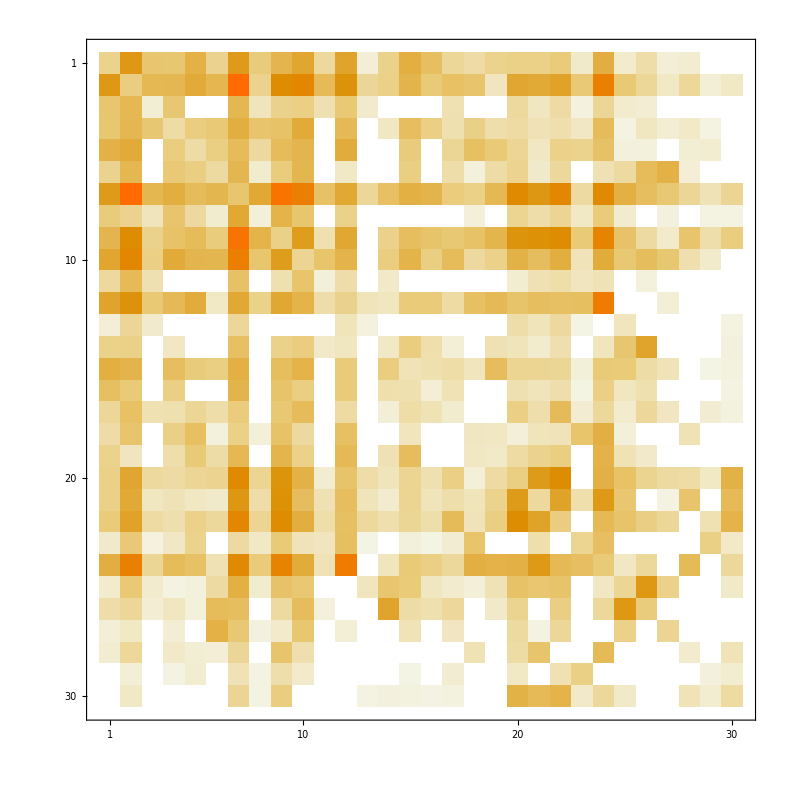

```mathematica
MatrixPlot[realmatrix]
```

```mathematica
md=DiagonalMatrix[Diagonal[realmatrix]];
```

```mathematica
mo=realmatrix-md
```

(0. | 0.100411 | 0.00665382 | 0.00637985 | 0.0267127 | 0.00276278 | 0.0908613 | 0.00504908 | 0.0214886 | 0.0544226 | 0.00187689 | 0.0584713 | 0.0000919287 | 0.00313141 | 0.0298708 | 0.0108214 | 0.00211839 | 0.00144282 | 0.00288639 | 0.00331719 | 0.00331659 | 0.00513908 | 0.000231414 | 0.030482 | 0.000187183 | 0.00134339 | 0.0000886355 | 0.000132726 | 0. | 0.
0.100411 | 0. | 0.0185239 | 0.0187331 | 0.0412177 | 0.0199525 | 0.366452 | 0.00274387 | 0.148858 | 0.181228 | 0.0149476 | 0.116517 | 0.00228734 | 0.00327864 | 0.0230818 | 0.00559302 | 0.010289 | 0.00765942 | 0.000487357 | 0.0524873 | 0.046304 | 0.0635697 | 0.00565612 | 0.229177 | 0.00571314 | 0.00216595 | 0.000386239 | 0.0020273 | 0.000087565 | 0.000351497
0.00665382 | 0.0185239 | 0. | 0.00603976 | 0. | 0. | 0.0193186 | 0.000559826 | 0.00293124 | 0.00355378 | 0.000891786 | 0.00566757 | 0.000188184 | 0. | 0. | 0. | 0.000891777 | 0. | 0. | 0.00183449 | 0.000482903 | 0.00145547 | 0.0000217942 | 0.00240679 | 0.000171026 | 0.000112269 | 0. | 0. | 0. | 0.
0.00637985 | 0.0187331 | 0.00603976 | 0. | 0.00429251 | 0.00564109 | 0.0320452 | 0.00769806 | 0.00951181 | 0.0432767 | 0. | 0.0159714 | 0. | 0.000406929 | 0.0113043 | 0.00362158 | 0.000951603 | 0.00350449 | 0.00114027 | 0.00147781 | 0.000772398 | 0.00102705 | 0.000389243 | 0.0139005 | 0.0000125906 | 0.0004601 | 0.000113019 | 0.000310598 | 9.73283×10^-6 | 0.
0.0267127 | 0.0412177 | 0. | 0.00429251 | 0. | 0.00367331 | 0.0145278 | 0.00175911 | 0.0143781 | 0.0216757 | 0. | 0.0357837 | 0. | 0. | 0.00492835 | 0. | 0.00239261 | 0.0107228 | 0.00546907 | 0.00244059 | 0.000415166 | 0.00315443 | 0.00286232 | 0.0101946 | 0.0000431516 | 0.0000433944 | 0. | 0.000108114 | 0.000127978 | 0.
0.00276278 | 0.0199525 | 0. | 0.00564109 | 0.00367331 | 0. | 0.0212576 | 0.000162768 | 0.00483515 | 0.0201448 | 0. | 0.000343861 | 0. | 0. | 0.00401148 | 0. | 0.00133435 | 0.0000417361 | 0.00138738 | 0.00272572 | 0.000206584 | 0.00191066 | 0. | 0.000865546 | 0.00161736 | 0.01401 | 0.0261592 | 0.000102857 | 0. | 0.
0.0908613 | 0.366452 | 0.0193186 | 0.0320452 | 0.0145278 | 0.0212576 | 0. | 0.0477806 | 0.316164 | 0.231903 | 0.00977862 | 0.0488052 | 0.0021888 | 0.0105059 | 0.0293013 | 0.0227596 | 0.00474434 | 0.00328069 | 0.0171877 | 0.163742 | 0.105286 | 0.179639 | 0.00156819 | 0.159369 | 0.0276205 | 0.0117342 | 0.00581163 | 0.00231293 | 0.000840854 | 0.00245616
0.00504908 | 0.00274387 | 0.000559826 | 0.00769806 | 0.00175911 | 0.000162768 | 0.0477806 | 0. | 0.0231667 | 0.00683838 | 0. | 0.00296831 | 0. | 0. | 0. | 0. | 0. | 0.0000740199 | 0. | 0.00265338 | 0.00128576 | 0.00263772 | 0.000351942 | 0.00520417 | 0.000146133 | 0. | 0.0000301708 | 0. | 0.0000139791 | 0.0000153561
0.0214886 | 0.148858 | 0.00293124 | 0.00951181 | 0.0143781 | 0.00483515 | 0.316164 | 0.0231667 | 0. | 0.086216 | 0.000964285 | 0.0491027 | 0. | 0.00322784 | 0.0117412 | 0.0089841 | 0.00597876 | 0.00931897 | 0.022533 | 0.113722 | 0.125886 | 0.149377 | 0.00553 | 0.197838 | 0.00917273 | 0.00161599 | 0.000190165 | 0.00760884 | 0.0011871 | 0.00448154
0.0544226 | 0.181228 | 0.00355378 | 0.0432767 | 0.0216757 | 0.0201448 | 0.231903 | 0.00683838 | 0.086216 | 0. | 0.00789433 | 0.0234023 | 0. | 0.00452523 | 0.0234192 | 0.00396582 | 0.0137391 | 0.00173337 | 0.00323817 | 0.0259689 | 0.0123843 | 0.030539 | 0.000664017 | 0.037372 | 0.00586241 | 0.0130097 | 0.0064159 | 0.000988816 | 0.000194112 | 0.
0.00187689 | 0.0149476 | 0.000891786 | 0. | 0. | 0. | 0.00977862 | 0. | 0.000964285 | 0.00789433 | 0. | 0.00126 | 0. | 0.000283693 | 0. | 0. | 0. | 0. | 0. | 0.000121788 | 0.00086735 | 0.00123291 | 0.000522635 | 0.000781099 | 0. | 0.0000374316 | 0. | 0. | 0. | 0.
0.0584713 | 0.116517 | 0.00566757 | 0.0159714 | 0.0357837 | 0.000343861 | 0.0488052 | 0.00296831 | 0.0491027 | 0.0234023 | 0.00126 | 0. | 0.000563003 | 0.000454148 | 0.00505938 | 0.00516886 | 0.00145453 | 0.010448 | 0.0164825 | 0.00808382 | 0.0111189 | 0.0106296 | 0.0107881 | 0.256729 | 0. | 0. | 0.0000770207 | 0. | 0. | 0.
0.0000919287 | 0.00228734 | 0.000188184 | 0. | 0. | 0. | 0.0021888 | 0. | 0. | 0. | 0. | 0.000563003 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00131041 | 0.000576306 | 0.00188899 | 1.82169×10^-6 | 0. | 0.000544096 | 0. | 0. | 0. | 0. | 0.0000130115
0.00313141 | 0.00327864 | 0. | 0.000406929 | 0. | 0. | 0.0105059 | 0. | 0.00322784 | 0.00452523 | 0.000283693 | 0.000454148 | 0. | 0. | 0.00415792 | 0.00108636 | 0.0000768077 | 0. | 0.000860571 | 0.000658588 | 0.000177614 | 0.00103976 | 0. | 0.000533343 | 0.00677217 | 0.0584084 | 0. | 0. | 0. | 0.0000355224
0.0298708 | 0.0230818 | 0. | 0.0113043 | 0.00492835 | 0.00401148 | 0.0293013 | 0. | 0.0117412 | 0.0234192 | 0. | 0.00505938 | 0. | 0.00415792 | 0. | 0.000939383 | 0.00134636 | 0.000536723 | 0.0132875 | 0.00250063 | 0.0026318 | 0.00240876 | 0.0000638361 | 0.005473 | 0.00525753 | 0.00139133 | 0.000710621 | 0. | 8.77489×10^-7 | 0.0000290155
0.0108214 | 0.00559302 | 0. | 0.00362158 | 0. | 0. | 0.0227596 | 0. | 0.0089841 | 0.00396582 | 0. | 0.00516886 | 0. | 0.00108636 | 0.000939383 | 0. | 0.000858278 | 0. | 0. | 0.000901801 | 0.000619673 | 0.00113403 | 2.53149×10^-6 | 0.00361868 | 0.000481799 | 0.000974095 | 0. | 0. | 0. | 5.31186×10^-6
0.00211839 | 0.010289 | 0.000891777 | 0.000951603 | 0.00239261 | 0.00133435 | 0.00474434 | 0. | 0.00597876 | 0.0137391 | 0. | 0.00145453 | 0. | 0.0000768077 | 0.00134636 | 0.000858278 | 0. | 0. | 0. | 0.00352766 | 0.00117771 | 0.014843 | 0.000114029 | 0.00198381 | 0.000175825 | 0.00204562 | 0.000438881 | 0. | 0.000120801 | 0.0000294816
0.00144282 | 0.00765942 | 0. | 0.00350449 | 0.0107228 | 0.0000417361 | 0.00328069 | 0.0000740199 | 0.00931897 | 0.00173337 | 0. | 0.010448 | 0. | 0. | 0.000536723 | 0. | 0. | 0. | 0.000423818 | 0.0000735881 | 0.000650968 | 0.000701546 | 0.00800521 | 0.0298126 | 0.0000547346 | 0. | 0. | 0.000843892 | 0. | 0.
0.00288639 | 0.000487357 | 0. | 0.00114027 | 0.00546907 | 0.00138738 | 0.0171877 | 0. | 0.022533 | 0.00323817 | 0. | 0.0164825 | 0. | 0.000860571 | 0.0132875 | 0. | 0. | 0.000423818 | 0. | 0.00146031 | 0.00289325 | 0.00389306 | 0. | 0.0243301 | 0.000855692 | 0.000266082 | 0. | 0. | 0. | 0.
0.00331719 | 0.0524873 | 0.00183449 | 0.00147781 | 0.00244059 | 0.00272572 | 0.163742 | 0.00265338 | 0.113722 | 0.0259689 | 0.000121788 | 0.00808382 | 0.00131041 | 0.000658588 | 0.00250063 | 0.000901801 | 0.00352766 | 0.0000735881 | 0.00146031 | 0. | 0.0937702 | 0.147339 | 0. | 0.0274627 | 0.00975335 | 0.0027375 | 0.00171445 | 0.00142336 | 0.000388607 | 0.0258641
0.00331659 | 0.046304 | 0.000482903 | 0.000772398 | 0.000415166 | 0.000206584 | 0.105286 | 0.00128576 | 0.125886 | 0.0123843 | 0.00086735 | 0.0111189 | 0.000576306 | 0.000177614 | 0.0026318 | 0.000619673 | 0.00117771 | 0.000650968 | 0.00289325 | 0.0937702 | 0. | 0.061665 | 0.00107383 | 0.0997137 | 0.00648635 | 0. | 0.000013675 | 0.00708145 | 0. | 0.0154644
0.00513908 | 0.0635697 | 0.00145547 | 0.00102705 | 0.00315443 | 0.00191066 | 0.179639 | 0.00263772 | 0.149377 | 0.030539 | 0.00123291 | 0.0106296 | 0.00188899 | 0.00103976 | 0.00240876 | 0.00113403 | 0.014843 | 0.000701546 | 0.00389306 | 0.147339 | 0.061665 | 0. | 0. | 0.0161243 | 0.00814184 | 0.00370964 | 0.00227517 | 0. | 0.000882877 | 0.0238534
0.000231414 | 0.00565612 | 0.0000217942 | 0.000389243 | 0.00286232 | 0. | 0.00156819 | 0.000351942 | 0.00553 | 0.000664017 | 0.000522635 | 0.0107881 | 1.82169×10^-6 | 0. | 0.0000638361 | 2.53149×10^-6 | 0.000114029 | 0.00800521 | 0. | 0. | 0.00107383 | 0. | 0. | 0.0107368 | 0. | 0. | 0. | 0. | 0.0035236 | 0.000280127
0.030482 | 0.229177 | 0.00240679 | 0.0139005 | 0.0101946 | 0.000865546 | 0.159369 | 0.00520417 | 0.197838 | 0.037372 | 0.000781099 | 0.256729 | 0. | 0.000533343 | 0.005473 | 0.00361868 | 0.00198381 | 0.0298126 | 0.0243301 | 0.0274627 | 0.0997137 | 0.0161243 | 0.0107368 | 0. | 0.000436091 | 0.00193697 | 0. | 0.014669 | 0. | 0.00191556
0.000187183 | 0.00571314 | 0.000171026 | 0.0000125906 | 0.0000431516 | 0.00161736 | 0.0276205 | 0.000146133 | 0.00917273 | 0.00586241 | 0. | 0. | 0.000544096 | 0.00677217 | 0.00525753 | 0.000481799 | 0.000175825 | 0.0000547346 | 0.000855692 | 0.00975335 | 0.00648635 | 0.00814184 | 0. | 0.000436091 | 0. | 0.100752 | 0.00313845 | 0. | 0. | 0.000239703
0.00134339 | 0.00216595 | 0.000112269 | 0.0004601 | 0.0000433944 | 0.01401 | 0.0117342 | 0. | 0.00161599 | 0.0130097 | 0.0000374316 | 0. | 0. | 0.0584084 | 0.00139133 | 0.000974095 | 0.00204562 | 0. | 0.000266082 | 0.0027375 | 0. | 0.00370964 | 0. | 0.00193697 | 0.100752 | 0. | 0. | 0. | 0. | 0.
0.0000886355 | 0.000386239 | 0. | 0.000113019 | 0. | 0.0261592 | 0.00581163 | 0.0000301708 | 0.000190165 | 0.0064159 | 0. | 0.0000770207 | 0. | 0. | 0.000710621 | 0. | 0.000438881 | 0. | 0. | 0.00171445 | 0.000013675 | 0.00227517 | 0. | 0. | 0.00313845 | 0. | 0. | 0. | 0. | 0.
0.000132726 | 0.0020273 | 0. | 0.000310598 | 0.000108114 | 0.000102857 | 0.00231293 | 0. | 0.00760884 | 0.000988816 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.000843892 | 0. | 0.00142336 | 0.00708145 | 0. | 0. | 0.014669 | 0. | 0. | 0. | 0. | 0. | 0.000767721
0. | 0.000087565 | 0. | 9.73283×10^-6 | 0.000127978 | 0. | 0.000840854 | 0.0000139791 | 0.0011871 | 0.000194112 | 0. | 0. | 0. | 0. | 8.77489×10^-7 | 0. | 0.000120801 | 0. | 0. | 0.000388607 | 0. | 0.000882877 | 0.0035236 | 0. | 0. | 0. | 0. | 0. | 0. | 0.000140144
0. | 0.000351497 | 0. | 0. | 0. | 0. | 0.00245616 | 0.0000153561 | 0.00448154 | 0. | 0. | 0. | 0.0000130115 | 0.0000355224 | 0.0000290155 | 5.31186×10^-6 | 0.0000294816 | 0. | 0. | 0.0258641 | 0.0154644 | 0.0238534 | 0.000280127 | 0.00191556 | 0.000239703 | 0. | 0. | 0.000767721 | 0.000140144 | 0.)

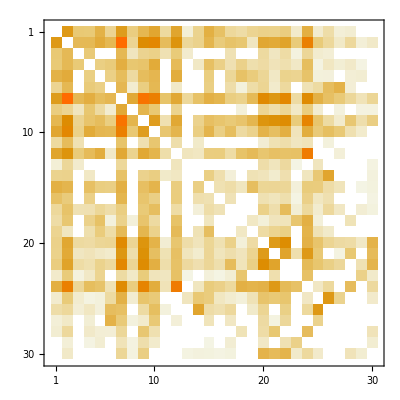

```mathematica
MatrixPlot[mo]
```

```mathematica
randommatrix=RandomReal[2,{30,30}];
```

```mathematica
ClearAll[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20,x21,x22,x23,x24,x25,x26,x27,x28,x29,x30]
```

```mathematica
listmember={x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20,x21,x22,x23,x24,x25,x26,x27,x28,x29,x30};
```

```mathematica
NMaximize[{Sum[Sum[listmember[[s]]*listmember[[t]]*mo[[s,t]],{t,1,30}],{s,1,30}],Sum[listmember[[i]],{i,1,6}]==2&&Sum[listmember[[i]],{i,7,19}]==4&&Sum[listmember[[i]],{i,20,29}]==4&&x30==1&&listmember∈Integers&&And@@Thread[0<=listmember≤1]},listmember,MaxIterations->200]
```

{8.87249,{x1→1,x2→1,x3→0,x4→0,x5→0,x6→0,x7→1,x8→0,x9→1,x10→1,x11→0,x12→1,x13→0,x14→0,x15→0,x16→0,x17→0,x18→0,x19→0,x20→1,x21→1,x22→1,x23→0,x24→1,x25→0,x26→0,x27→0,x28→0,x29→0,x30→1}}

```mathematica
Sum[Sum[listmember[[s]]*listmember[[t]]*randommatrix[[s,t]],{t,1,30}],{s,1,30}];
```

```mathematica
{8.911666775425507,{x1->1,x2->1,x3->0,x4->0,x5->0,x6->0,x7->1,x8->0,x9->1,x10->1,x11->0,x12->1,x13->0,x14->0,x15->0,x16->0,x17->0,x18->0,x19->0,x20->1,x21->1,x22->1,x23->0,x24->1,x25->0,x26->0,x27->0,x28->0,x29->0,x30->1}}
```